The actual data is known and predetermined:

```mathematica
class1:={1,0}
```

```mathematica
class2:={0,1}
```

For an arbitrary point in the plane we can specify that its class is that of the center closest to it.

```mathematica
distanceclass[p_]:=EuclideanDistance[p,class1]-EuclideanDistance[p,class2]
```

We can plot the centers of the classes and the decision boundary.

```mathematica
color1=ColorData[97,"ColorList"][[1]];
```

```mathematica
color2=ColorData[97,"ColorList"][[2]];
```

```mathematica
boundarystyle={Magenta,Dashed};
```

```mathematica
rangex:={x,-2.6,4.2}
```

```mathematica
rangey:={y,-2,2.9}
```

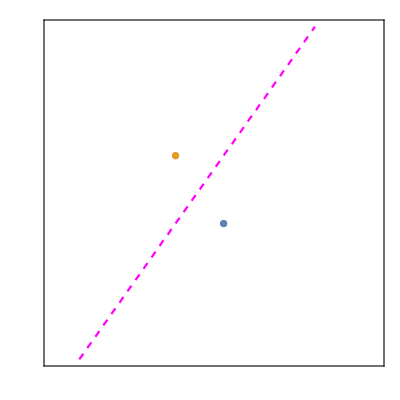

```mathematica
Show[ListPlot[{{class1},{class2}},PlotRange->{rangex[[2;;]],rangey[[2;;]]},Axes->False,Frame->True,FrameTicks->None,AspectRatio->1,FrameStyle->RGBColor[7/8,7/8,7/8]],ContourPlot[distanceclass[{x,y}]==0,rangex,rangey,Axes->False,Frame->False,ContourStyle->boundarystyle]]
```

For each point in the plane we can also show which class it belongs to. For this we define a grid which will also be used in the other visualizations.

```mathematica
grid=Flatten[Table[{x,y},Evaluate[Append[rangex,0.1]],Evaluate[Append[rangey,0.1*4.9/6.8]]],1];
```

Given the distance function defined above we assign the based on the function being positive or negative.

```mathematica
colordistance[p_]:=If[distanceclass[p]≤ 0,color1,color2];
```

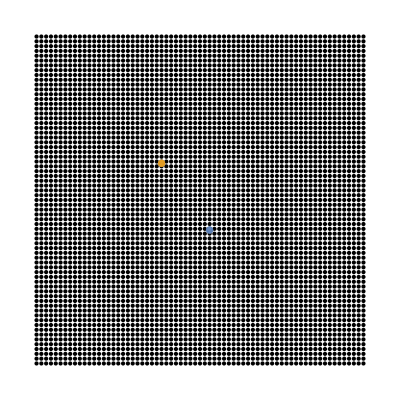

```mathematica
Show[Graphics[Point[grid,VertexColors->colordistance/@grid],AspectRatio->1],ListPlot[{{class1},{class2}},PlotRange->{rangex[[2;;]],rangey[[2;;]]},Axes->False,Frame->True,FrameTicks->None,AspectRatio->1,FrameStyle->RGBColor[7/8,7/8,7/8]]]
```

The actual measurements are different. The are generated with a multi-normal distribution around the actual values with standard deviation 1/5 in both dimensions

```mathematica
stdev:=1/5
```

The samples are summarized by their means:

```mathematica
ESLmeans = Import["https://raw.githubusercontent.com/drepper/ESL/master/ESL-mixture-means.csv", "HeaderLines" -> 1];
```

For convenience, split the data set for the two classes and just keep the coordinates

```mathematica
ESLmeans1=ESLmeans[[1;;10,2;;3]];
```

```mathematica
ESLmeans2=ESLmeans[[11;;20,2;;3]];
```

We can visualize the actual data (unfilled circles) and the measurements (filled circles)

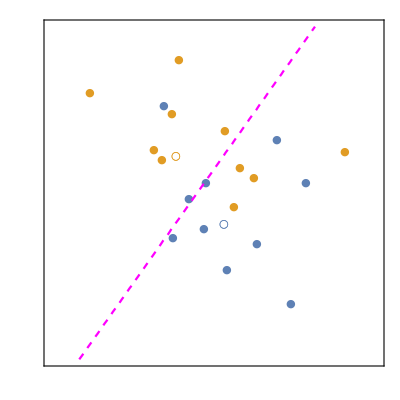

```mathematica
Show[ListPlot[{ESLmeans1,ESLmeans2,{class1},{class2}},PlotRange->{rangex[[2;;]],rangey[[2;;]]},AspectRatio->1,Axes->False,Frame->True,FrameTicks->None,FrameStyle->RGBColor[7/8,7/8,7/8],PlotStyle->{color1,color2,color1,color2},PlotMarkers->{"●","●","○","○"}],ContourPlot[distanceclass[{x,y}]==0,rangex,rangey,Axes->False,Frame->False,ContourStyle->boundarystyle]]
```

We can see that the ideal decision boundary does not divide the actual means of the measurements nicely. This is expected.

Given that we know the standard deviation of the measurements we can determine the maximum contained information in the measurement. For each point in the plane we can determine the likelihood that an instantiation at that location is the result from the actual individual measurements. Adding all the likelihoods we can determine whether a measurement at a specific location is more likely in one or the other class.

```mathematica
distancebayes[p_,m_]:=Total[Map[Function[c,PDF[MultinormalDistribution[c,IdentityMatrix[2]*stdev],p]],m]]
```

```mathematica
classbayes[p_]:=distancebayes[p,ESLmeans1]-distancebayes[p,ESLmeans2]
```

```mathematica
bayesboundary=ContourPlot[classbayes[{x,y}]==0,rangex,rangey,Axes->False,Frame->False,ContourStyle->boundarystyle];
```

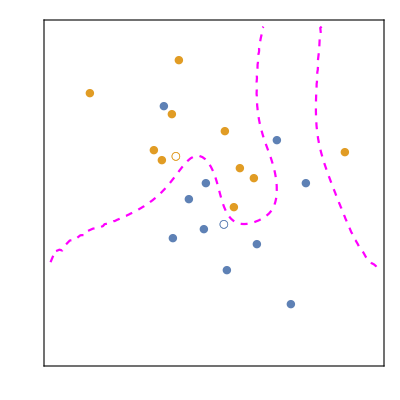

```mathematica
Show[ListPlot[{ESLmeans1,ESLmeans2,{class1},{class2}},PlotRange->{rangex[[2;;]],rangey[[2;;]]},AspectRatio->1,Axes->False,Frame->True,FrameTicks->None,FrameStyle->RGBColor[7/8,7/8,7/8],PlotStyle->{color1,color2,color1,color2},PlotMarkers->{"●","●","○","○"}],bayesboundary]
```

This is the optimal information we can extract from the measurements. It is a far cry from the exact boundary of the real data but with the uncertainty involved in the instantiation and the measurement this is what all other models can strive for.